```mathematica
SetDirectory[NotebookDirectory[]];
```

## Set wire data

```mathematica
r=0.127;
a=0.14296223129593358;
b=0.077709367530352944;
b=a;
a=0.077709367530352944;
n=128;
dt=(2π)/n;
```

```mathematica
a>b
```

False

```mathematica
cdata=Table[{r Cos[t],r Sin[t]},{t,0,2π,dt}]//N;
data=Table[{ a Cos[t],b Sin[t]},{t,0,2π,dt}]//N;
bcdata={};
For[i=0,i<=n,i++,
t=i*dt;
x={ a Cos[t],b Sin[t] };
If[Norm[x]<r,
If[a>b,
ts=ArcCos[(a/r)Cos[t]];
AppendTo[bcdata,{r Cos[ts],Sign[b Sin[t]]r Sin[ts]}];
,
ts=ArcSin[(b/r)Sin[t]];
AppendTo[bcdata,{Sign[a Cos[t]]r Cos[ts],r Sin[ts]}];
];
,
AppendTo[bcdata,x];
];
];
```

```mathematica
Length[data]
```

129

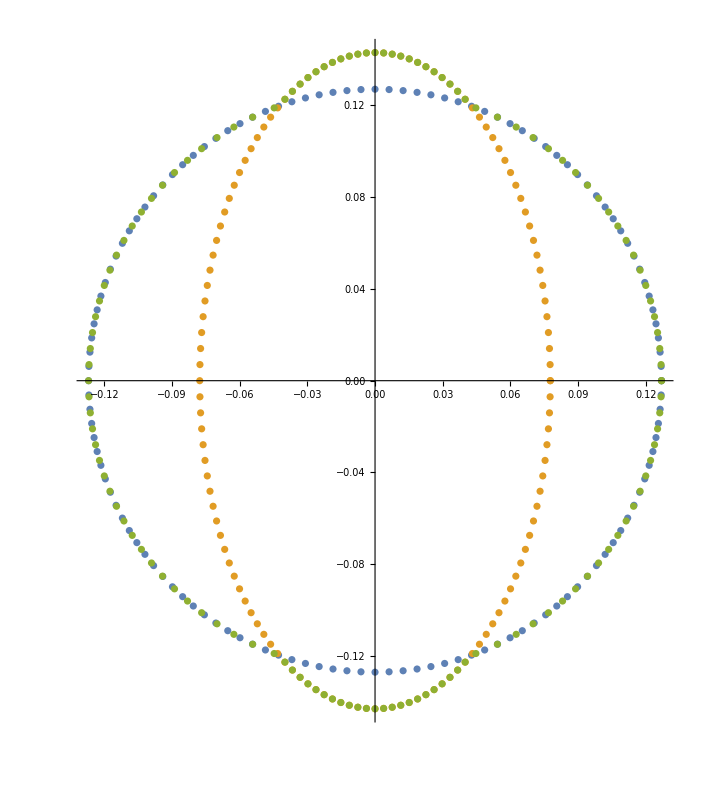

```mathematica
ListPlot[{cdata,data,bcdata},AspectRatio->Automatic,Joined->{False,False}]
```

Appending third coordinate

```mathematica
data=Table[{data[[i,1]],data[[i,2]],0.0},{i,1,Length[data]-1}];
```

## Exporting wire

```mathematica
(*Export["internal_wire.dat",data];*)
```